Phase Estimation circuit approximates a phase of a given operator using a number of auxiliary (counting) qubits.

For example the following circuit estimates phase (2π)/8, which is the phase of the T operator, with 5 qubits:

```mathematica
QuantumOperator[{"Phase",2Pi/8}]==QuantumOperator["T"]
```

True

```mathematica
circuit=QuantumCircuitOperator[{"PhaseEstimation",QuantumOperator[{"Phase",2Pi/8},"Label"->"U"],5}];
```

```mathematica
circuit["Diagram",FontSize->12]
```

-Graphics-

Operators powers can be expanded with "PowerExpand"→True:

```mathematica
QuantumCircuitOperator[{"PhaseEstimation",QuantumOperator[{"Phase",2Pi/8},"Label"->"U"],3,"PowerExpand"->True}]["Diagram",FontSize->12]
```

-Graphics-

```mathematica
QuantumCircuitOperator[{"PhaseEstimation",QuantumOperator[{"Phase",2Pi/8}],3,"PowerExpand"->True}]==QuantumCircuitOperator[{"PhaseEstimation",QuantumOperator[{"Phase",2Pi/8}],3,"PowerExpand"->False}]
```

True

Because fraction 1/8 has an exact binary representation using 5 bits (even 3 bits is enough), there is 100% probability of measuring 00100 state.

```mathematica
circuit[]
```

QuantumMeasurement[…]

```mathematica
TakeLargest[%["Probabilities"],3]
```

<|00100→1,00010→0,00001→0|>

For different phases between 0 and 2π there are different probability distributions:

```mathematica
phases=Range[0,.96,0.05]
```

{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95}

```mathematica
measurements=ParallelTable[QuantumCircuitOperator[{"PhaseEstimation",QuantumOperator[{"Phase",2Pi phase}],5}][],{phase,phases}];
```

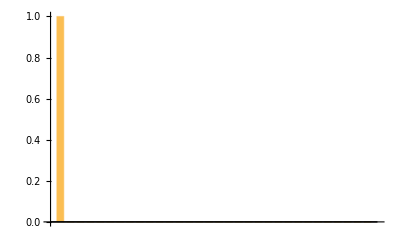
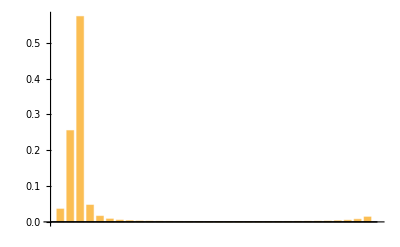
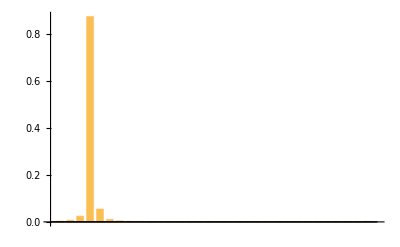
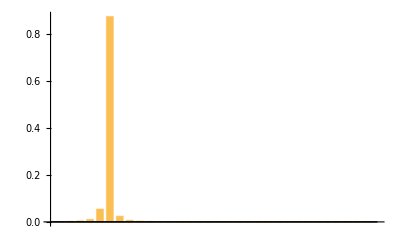
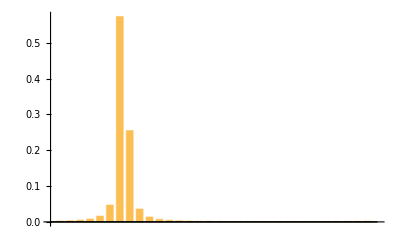
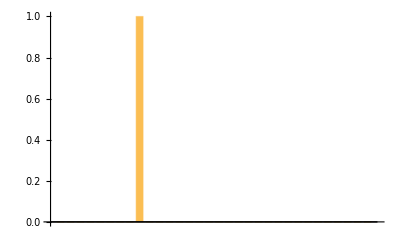
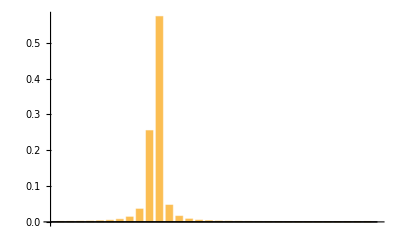
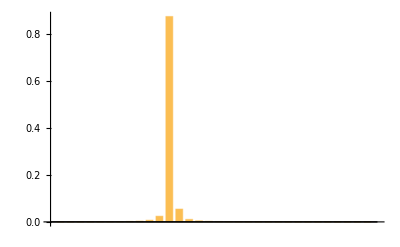

```mathematica
BarChart[#["Probabilities"]]&/@measurements
```

Even though there is good chance to approximate a phase with a single measurement, getting an average would significantly improve its estimate:

```mathematica
predMode=Last[KeyValueMap[#2#1/2^5&]@Sort[KeyMap[FromDigits[#["Name"],2]&]@#["Probabilities"]]]&/@measurements
```

{0.,0.0358176,0.0820549,0.136758,0.107453,0.25,0.179088,0.300868,0.355571,0.250723,0.5,0.322358,0.519681,0.574385,0.393993,0.75,0.465628,0.738494,0.793198,0.537264}

```mathematica
predMean=Total[KeyValueMap[#2#1/2^5&]@KeyMap[FromDigits[#["Name"],2]&]@#["Probabilities"]]&/@measurements
```

{0.,0.095176,0.104255,0.160709,0.208239,0.25,0.308802,0.346812,0.405662,0.448051,0.5,0.551043,0.593965,0.652763,0.689849,0.75,0.789204,0.837654,0.892212,0.868729}

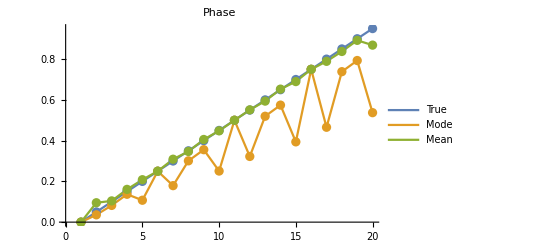

```mathematica
ListLinePlot[{phases,predMode,predMean},PlotLabel->"Phase",Mesh->All,PlotLegends->{"True","Mode","Mean"}]
```

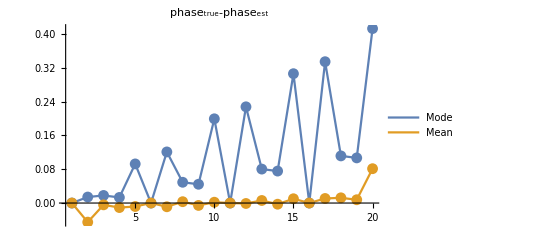

```mathematica
ListLinePlot[{phases-predMode,phases-predMean},PlotLabel->"phase_true-phase_est",Mesh->All,PlotRange->Full,PlotLegends->{"Mode","Mean"}]
```

A couple of questions that one can immediately raise here:

Is there a better estimator (maybe even an unbiased one) of phase from a measurement distribution obtained this way?
What is the trade-off between increasing number of samples and increasing number of qubits?